```mathematica
Clear[r1,K1,a1,h1,eps1,eps2,e1,c1,p1,L1 ,r2,K2,a1,a2,h2,e2,c2,p2,L2 ,P1,P2,curve1]
r1:=1;r2:=1;K1:=500;K2:=500;a1:=0.9;a2:=0.9;eps1:=0.1;eps2:=0.1;h1:=50;h2:=50;e1:=50;e2:=50;L1:=50;L2:=50; curve1={{0,0}};curve2={{0,0}};surf1={};surf2={};
```

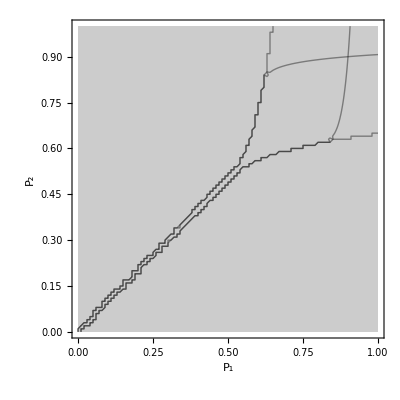

```mathematica
Do[
{sol=NDSolve[{
N1'[t]==r1*N1[t]*(1-N1[t]/K1)-(1-P1)a1*N1[t]*N2[t]/(e1+N1[t])+P1*eps1*N1[t]*N2[t]/(h2+N2[t]),
N2'[t]==r2*N2[t]*(1-N2[t]/K2)-(1-P2)a2*N1[t]*N2[t]/(e2+N2[t])+P2*eps2*N1[t]*N2[t]/(h1+N1[t]),
N1[0]==500,N2[0]==500},{N1,N2},{t,0,100}],
AppendTo[surf1,{P1,P2,Extract[Evaluate[N1[100]/.sol],{1}]}],
AppendTo[surf2,{P1,P2,Extract[Evaluate[N2[100]/.sol],{1}]}]
}, {P1,0,1,0.01},
{P2,0,1,0.01}
]

S1=ListContourPlot[{surf1,surf2},Mesh->None,Contours->{K1-0.001,0.001},FrameLabel->{Subscript[P, 1],Subscript[P, 2]},ContourShading->None]
```

```mathematica
ListPlot3D[surf1,Mesh->None,AxesLabel->{Subscript[P, 1],Subscript[P, 2],Subscript[N, 1] },PlotRange->All]
ListPlot3D[surf2,Mesh->None,AxesLabel->{Subscript[P, 1],Subscript[P, 2],Subscript[N, 2]},PlotRange->All]
```

-Graphics3D-

-Graphics3D-